Piecewise[{{20, -1/20≤x≤1/20}, {0, True}}]

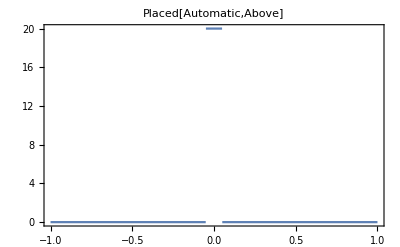

```mathematica
delta2[x_]=Piecewise[{{20,-5/100<=x≤5/100},{0,Abs[x]>5/100}}]
plot1=Plot[delta2[x],{x,-1,1},
PlotLabel->Placed[Automatic,Above],Frame->True]
```

Piecewise[{{1, -1/2≤x≤1/2}, {0, True}}]

Sinc[5 π t] UnitStep[4-t^2]

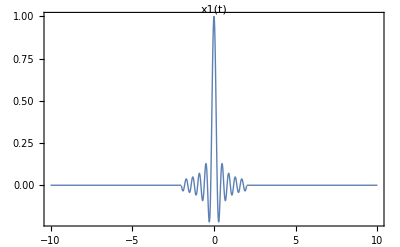

```mathematica
Piecewise[{{1, -1/2≤x≤1/2}, {0, True}}]
x1[x_]=Sinc[5*(Pi)*t]*UnitStep[4-t^2]
plot1=Plot[x1[t],{t,-10,10},PlotLabels->Placed[Automatic,Above],PlotStyle->Thick,Frame->True]
```

Ramp[4-t^2] UnitStep[Sin[π t]]

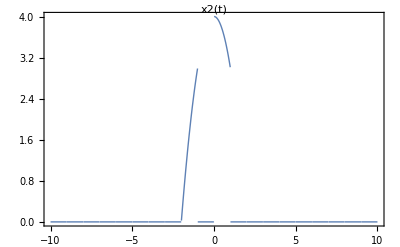

```mathematica
x2[x_]=UnitStep[Sin[(Pi)*t]]*Ramp[4-t^2]
plot2=Plot[x2[t],{t,-10,10},PlotLabels->Placed[Automatic,Above],PlotStyle->Thick,Frame->True]
```

Piecewise[{{0, t<-1}, {1, -1<t<0}, {ⅇ^(-t/2), 0<t}, {0, True}}]

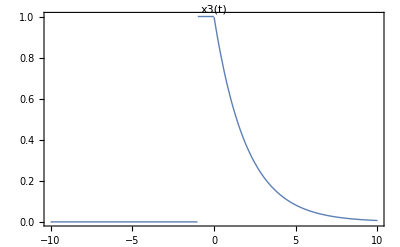

Piecewise::pairs: The first argument {{0,True},{1,False},{148.383}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {{0.,True},{1.,False},{148.383}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {{0.,True},{1.,False},{120.991}} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

```mathematica
x3[x_]=Piecewise[{{0,t<-1},{1,-1<t<0},{Exp[-1/2*t],0<t}}]
plot3=Plot[x3[t],{t,-10,10},PlotLabels->Placed[Automatic,Above],PlotStyle->Thick,Frame->True,PlotRange->Full]
```

(Piecewise[{{1, -1/10≤-3+t≤1/10}, {0, True}}])+2 (Piecewise[{{1, -1/10≤1+t≤1/10}, {0, True}}])

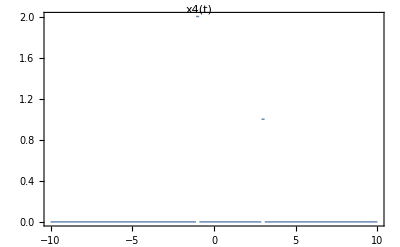

```mathematica
x4[x_]=delta2[t-3]+2delta2[t+1]
plot2=Plot[x4[t],{t,-10,10},PlotLabels->Placed[Automatic,Above],PlotStyle->Thick,Frame->True,PlotRange->Full]
```

(ⅇ^(-t^2/2))/(√(2 π))

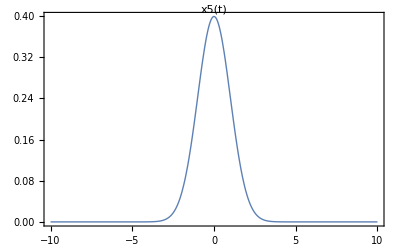

```mathematica
x5[x_]=1/(√(2π))*Exp[-1/2*t^2]
plot2=Plot[x5[t],{t,-10,10},PlotLabels->Placed[Automatic,Above],PlotStyle->Thick,Frame->True,PlotRange->Full]
```

```mathematica
eng[x_]=Integrate[(x)^2,{t,-Infinity,+Infinity}]
eng[x1[t]]
eng[x2[t]]
eng[x3[t]]
eng[x4[t]]
eng[x5[t]]

pow[x_]=Limit[1/T Integral[(x)^2],T->+Infinity ]
pow[x1[t]]
pow[x2[t]]
pow[x3[t]]
pow[x4[t]]
pow[x5[t]]
```

Integrate::idiv: Integral of x^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ x^2 ⅆt

(2 SinIntegral[20 π])/(5 π)

256/15

2

1

1/(2 √π)

Table::itraw: Raw object 1 cannot be used as an iterator.

```mathematica
Table[eng[i],{i,{x1[t],x2[t],x3[t],x4[t],x5[t]}}]
```

{(2 SinIntegral[20 π])/(5 π),256/15,2,1,1/(2 √π)}

```mathematica
Table[pow[i],{i,{x1[t],x2[t],x3[t],x4[t],x5[t]}}]
```

```mathematica
{0,0,0,0,0}
dcfunc[x_]=Integrate[(x),{t,-Infinity,+Infinity}]
Table[dcfunc[i],{i,{x1[t],x2[t],x3[t],x4[t],x5[t]}}]
```

{0,0,0,0,0}

Integrate::idiv: Integral of x does not converge on {-∞,∞}.

∫_(-∞)^∞ xⅆt

{(2 SinIntegral[10 π])/(5 π),16/3,3,3/5,1}

```mathematica
dcfunc[x_]=Limit[1/T Integral[x],T->+Infinity ]
Table[dcfunc[i],{i,{x1[t],x2[t],x3[t],x4[t],x5[t]}}]
```

0

```mathematica
{0,0,0,0,0}
x6[x_]=Sin[t]+0.5Sin[3t];
```

{0,0,0,0,0}

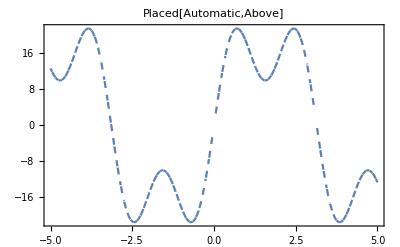

```mathematica
xs[x_]=Sum[x6[0.1n]*delta2[t-0.1n],{n,-50,+50}];
plot2=Plot[xs[t],{t,-5,+5},Frame->True,PlotRange->Full,PlotLabel->Placed[Automatic,Above],PlotStyle->Dashed]
```

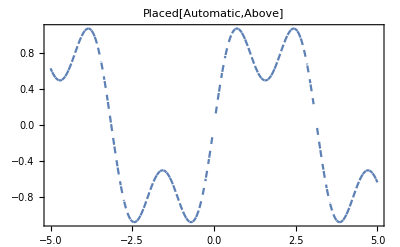

```mathematica
Show[plot2,AxesStyle->Directive[RGBColor[1.,0.,0.20689707789730677],AbsoluteThickness[1]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

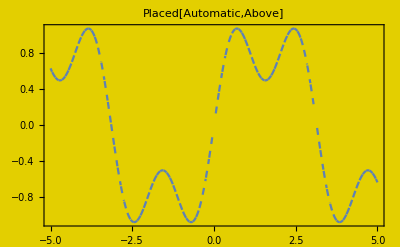

```mathematica
Show[%29,Background->RGBColor[0.89,0.81,0.]]
```